```mathematica
ϵ[r_]:=(T+α/r)/(m*c^2);
```

```mathematica
f[r_]:=(2*ϵ[r]+ϵ[r]^2)/(1+ϵ[r])^2-α^2/(l^2*c^2)*((l^2/(m*α*r))^2)/(1+ϵ[r])^2;
```

```mathematica
∫(Sqrt[(1-f[1/u])/(f[1/u]*(1+u^2*p^2*ζ))]*p^2*ζ*u)ⅆu//FullSimplify
```

p^2 ζ ∫u √((c^4 m^2+c^2 l^2 u^2)/(((T+u α)^2+c^2 (-l^2 u^2+2 m (T+u α))) (1+p^2 u^2 ζ)))ⅆu

```mathematica
g[r_]:=(1-(1+l^2/(m^2*c^2*r^2))*((m*c^2)/(T+m*c^2+α/r))^2);
```

```mathematica
g[r]//FullSimplify
```

1-(c^2 (l^2+c^2 m^2 r^2))/((c^2 m r+r T+α)^2)

```mathematica
f[r]//FullSimplify
```

1-(c^2 (l^2+c^2 m^2 r^2))/((c^2 m r+r T+α)^2)

(c m r (c^4 l^2 m r+c^6 m^3 r^3+2 (r T+α)^3))/((r T+α) (c^4 m^2 r^2+(r T+α)^2))==0

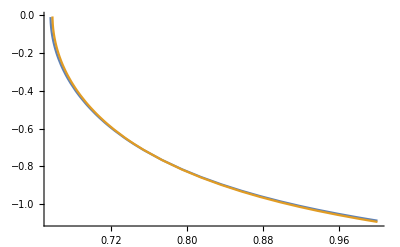

```mathematica
l=1;
a=1;
m=1;
α=0.1;
m=1;
T=1;
c=10;
ζ=α^2/(l^2*c^2);
p=l^2/(m*α);
Gal[r_]:=-Sqrt[(2*α)/(m*r)+(2*T)/m-ζ*((p*c)/r)^2];
Plot[{fEl[r],Gal[r]},{r,0,1},PlotRange->All]
```

```mathematica
Limit[fEl[r],r-> 0]
```

0.-999.95 ⅈ

```mathematica
(En*r+mass*)
```

```mathematica
fEl[r_]:=Sqrt[(1-(1+ζ*(p^2/r^2))*(1/(ϵ[r]+1))^2)];
```

```mathematica
∫(Sqrt[(1-fEl[1/u])/(fEl[1/u]*(1+u^2*p^2*ζ))]*p^2*ζ*u)ⅆu//FullSimplify
```

p^2 ζ ∫u √((1-√(1-(c^4 m^2 (1+p^2 u^2 ζ))/((c^2 m+T+u α)^2)))/((1+p^2 u^2 ζ) √(1-(c^4 m^2 (1+p^2 u^2 ζ))/((c^2 m+T+u α)^2))))ⅆu

```mathematica
fEl'[r]//FullSimplify
```

(c^4 m^2 (-r α+p^2 (c^2 m+T) ζ))/((c^2 m r+r T+α)^3 √(1-(c^4 m^2 (r^2+p^2 ζ))/((c^2 m r+r T+α)^2)))

```mathematica
Sqrt[(1-fEl[r])/(fEl[r]*(1+(p/r)^2*ζ))]*((p/r)^2*ζ)*1/r//FullSimplify
```

(p^2 ζ √(-(r^2 (-1+√(1-(c^4 m^2 (r^2+p^2 ζ))/((c^2 m r+r T+α)^2))))/((r^2+p^2 ζ) √(1-(c^4 m^2 (r^2+p^2 ζ))/((c^2 m r+r T+α)^2)))))/r^3

```mathematica
DSolve[u''[ϕ]+(1-ζ)*u[ϕ]== s,u,ϕ]
```

{{u→Function[{ϕ},s/(1-ζ)+ⅇ^(√(-1+ζ) ϕ) C[1]+ⅇ^(-√(-1+ζ) ϕ) C[2]]}}

```mathematica
(D[s/(1-ζ)+ⅇ^(√(-1+ζ) ϕ) C[1]+ⅇ^(-√(-1+ζ) ϕ) C[2],{ϕ,2}]+(1-ζ)*(s/(1-ζ)+ⅇ^(√(-1+ζ) ϕ) C[1]+ⅇ^(-√(-1+ζ) ϕ) C[2]))//FullSimplify
```

s

```mathematica
Clear["Global`*"]
```

```mathematica
r=1/(((α*E)/(c^2*l^2)+(m*α)/l^2)/(1-α^2/(l^2*c^2))+A);
```

```mathematica
Solve[(c^2*l^2)/r^2+m^2*c^2== (E+m*c^2+α/r)^2,A]//FullSimplify
```

{{A→-(√((c^2 (l^2 (ⅇ+(-1+c) c m) (ⅇ+c (1+c) m)+m^2 α^2))/((c l-α) (c l+α))))/(√((c l-α) (c l+α)))},{A→(√((c^2 (l^2 (ⅇ+(-1+c) c m) (ⅇ+c (1+c) m)+m^2 α^2))/((c l-α) (c l+α))))/(√((c l-α) (c l+α)))}}

```mathematica
(c^2 (l^2 (ⅇ+(-1+c) c m) (ⅇ+c (1+c) m)+m^2 α^2))/(l^2*c^2)//Expand
```

ⅇ^2+2 c^2 ⅇ m-c^2 m^2+c^4 m^2+(m^2 α^2)/l^2

```mathematica
Limit[(Sqrt[(ⅇ^2+2 c^2 ⅇ m-c^2 m^2+c^4 m^2+(m^2 α^2)/l^2)/((α*E)/(c^2*l^2)+(m*α)/l^2)^2]),c-> ∞]//FullSimplify
```

DirectedInfinity[√(Sign[l]^4/Sign[α]^2)]